# Zestaw 7

## Zadanie 1. Całki po konturze, całka niezorientowana, Integrate, ParametricPlot, Norm, Region, NIntegrate, LineIntegrate

Oblicz całkę  z funkcji   po eliptycznym konturze  zadanym przez elipsę o półosiach  oraz .
Zadana całka to całka niezorientowana, tj. nie ma znaczenia kierunek całkowania po krzywej, argument funkcji  to , a funkcja zwraca wartość ze zbioru .
Z kolei,  może być intuicyjnie rozumiane jako element długości krzywej.

```mathematica
f[{x_, y_}] := x^2 + y^2
```

W celu obliczenia zadanej całki wykonaj następujące polecenia:

### 1) Sparametryzuj elipsę korzystając ze związku dla

Narysuj tę elipsę korzystając z ParametricPlot

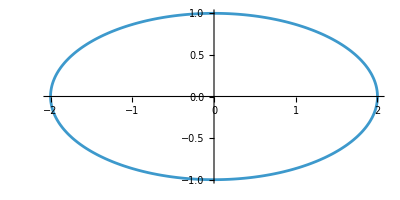

```mathematica
{rx, ry} = {2, 1};
{tMin, tMax} = {0, 2π};

c[t_] := {rx * Cos[t], ry * Sin[t]}

ParametricPlot[c[t], {t, tMin, tMax}]
```

### 2) Następnie wykorzystując tę parametryzację oblicz całkę korzystając ze wzoru

```mathematica
Integrate[
f[ c[t] ] Norm[ c'[t] ],
{t, tMin, tMax}
]
```

4/3 (5 EllipticE[-3]+4 EllipticK[-3])

### 3) Zdefiniuj obszar będący zadaną elipsą korzystając z poleceń Region oraz Circle

```mathematica
reg = Circle[{0, 0}, {rx, ry}]
```

Circle[{0,0},{2,1}]

```mathematica
Integrate[f[xy],xy ∈ reg]
```

4/3 (5 EllipticE[-3]+4 EllipticK[-3])

### 4) Wykonaj obliczenia z 3) również numerycznie korzystając z NIntegrate

O ile szybciej wykonały się obliczenia? Jaka jest różnica wyników?

```mathematica
NIntegrate[f[xy],xy ∈ reg]
```

21.8981

### 5) Oblicz całkę korzystając z funkcji LineIntegrate

```mathematica
?LineIntegrate
```

```mathematica
LineIntegrate[f[xy], xy ∈ reg]
```

4/3 (5 EllipticE[-3]+4 EllipticK[-3])

## Zadanie 2. Całki po konturze, całka zorientowana, Integrate, StreamPlot, ParametricRegion

```mathematica
v[{x_, y_}] := {x y, x^2 + y^2}

c[t_] := {Cos[t], Sin[2t]}
```

### 1) Narysuj zadaną krzywą przy użyciu ParametricPlot

Jest to tzw. krzywa Lissajous.

Korzystając z opcji ColorFunction -> (Hue[#3]&) przedstaw na tym wykresie wartość .

```mathematica
lissajousPlot = ParametricPlot[
c[t],
{t, 0, 2π},
ColorFunction->(Hue[#3]&)
]
```

-Graphics-

### 2) Przedstaw na tym samy wykresie pole wektorowe korzystając z funkcji StreamPlot

```mathematica
?StreamPlot
```

```mathematica
Show[
lissajousPlot,
StreamPlot[
v[{x, y}],
{x, -1, 1},
{y, -1, 1}
]
]
```

-Graphics-

### 3) Następnie wykorzystując parametryzację oblicz zadaną całkę korzystając ze wzoru

```mathematica
Integrate[
v [ c[t] ] .  c'[t],
{t, 0, 2π}
]
```

π/2

### 4) Oblicz całkę korzystając z funkcji LineIntegrate oraz ParamtericRegion

```mathematica
region = ParametricRegion[c[t], {{t, 0, 2π}}]
```

ParametricRegion[{{Cos[t],Sin[2 t]},0≤t≤2 π},{t}]

```mathematica
LineIntegrate[v[xy], xy ∈ region]
```

π/2

## Zadanie 3. Praca w polu grawitacyjnym, Integrate, Assumptions, Expand, ParametricPlot3D

Na punktową cząstkę o masie  w polu grawitacyjnym masy  działa siła .
Oblicz pracę wykonaną przez siłę dla cząstki zaczynającej ruch w punkcie  gdzie , a kończącej w punkcie  gdzie  dla drogi zadanej przez:

```mathematica
F[{x_,y_,z_}]:= -G M m {x, y, z} / (x^2 + y^2 + z^2) ^(3/2)
```

```mathematica
FullSimplify[F[{r, 0, 0}][[1]]]
```

-(G m M r)/((r^2)^(3/2))

#### 1) krzywą

```mathematica
{tMin, t1Max} = {0, 5π/2};
```

```mathematica
c1[t_] := {a Cos[t], b Sin[t], t (t - t1Max)}
```

Wykonując całkę użyj założeń, tj. w funkcji Integrate zastosuj Assumptions -> {a > 0, b > 0}
(sprawdź jaki wynik uzyskasz bez tych założeń).

```mathematica
W1 = Integrate[
F[ c1[t] ] . c1'[t],
{t, tMin, t1Max}
]
```

-((1/(√(a^2))-1/(√(b^2))) G m M)

```mathematica
W1 = Integrate[
F[ c1[t] ] . c1'[t],
{t, tMin, t1Max},
Assumptions -> {a > 0, b > 0}
]
```

((a-b) G m M)/(a b)

Uprość wyrażenie przez użycie funkcji Expand.

```mathematica
Expand[W1]
```

-(G m M)/a+(G m M)/b

#### 2) Podobnie oblicz pracę wykonaną wzdłuż drogi zadanej przez krzywą

```mathematica
t2Max =9π/2 ;

c2[t_] := {a Cos[t], b Sin[t], t (t - t2Max)}

W2 = Integrate[
F[ c2[t] ] . c2'[t],
{t, tMin, t2Max},
Assumptions -> {a > 0, b > 0}
]
```

((a-b) G m M)/(a b)

```mathematica
Expand[W2]
```

-(G m M)/a+(G m M)/b

### 3) Przedstaw krzywe oraz na wykresie ParametricPlot3D

```mathematica
workPlots[a0_, b0_] := Show[
ParametricPlot3D[
c2[t] /. {a -> a0, b -> b0},
{t, tMin, t2Max},
PlotStyle-> Orange
],
ParametricPlot3D[
c1[t] /. {a -> a0, b -> b0},
{t, tMin, t1Max},
PlotStyle-> Blue
]
];

Manipulate[
Legended[
workPlots[a0, b0],
LineLegend[{Blue, Orange},{"c1(t)","c2(t)"}]
],
{{a0, 10, "a"}, 0, 20},
{{b0, 10, "b"}, 0, 20}
]
```

Porównaj pracę  z .
Od czego zależy praca wykonana w polu grawitacyjnym?
Odp. Od różnicy energii w punkcie końcowym i początkowym.

## Zadanie 4). Środek ciężkości, RegionPlot, ImplicitRegion, Area, SurfaceIntegrate, RegionCentroid

Wyznaczyć środek ciężkości  dla obszaru

```mathematica
f1[x_] := x^4
f2[x_] := x^(1/4)

{xMin, xMax} = {0, 1};
```

#### 1) Narysować obie funkcje oraz zaznaczyć interesujący nas obszar

Można użyć Show oraz RegionPlot, albo skorzystać z opcji Filling -> {1 -> {2}} dla Plot.

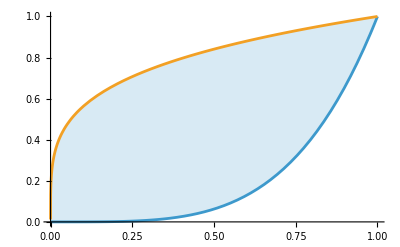

```mathematica
Plot[
{f1[x], f2[x]},
{x, xMin, xMax},
Filling -> {1 -> {2}}
]
```

Sprawdź, jak zmieni się efekt wypełnienia obszaru dla Filling -> {2 -> {1}}

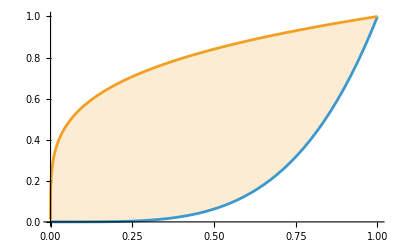

```mathematica
Plot[
{f1[x], f2[x]},
{x, xMin, xMax},
Filling -> {2 -> {1}}
]
```

#### 2) Obliczyć pole powierzchni zadanego obszaru

#### Sposób I

```mathematica
S = Integrate[f2[x] - f1[x], {x, xMin, xMax}]
```

3/5

#### Sposób II

```mathematica
Integrate[1,{x, xMin, xMax},{y, f1[x], f2[x]}]
```

3/5

#### Sposób III

```mathematica
reg = ImplicitRegion[
xMin <= x <= xMax && f1[x] <= y <= f2[x],
{x, y}
];

Area[reg]
```

3/5

#### Sposób IV

```mathematica
Integrate[1, {x, y} ∈ reg]
```

3/5

#### Sposób V

```mathematica
?SurfaceIntegrate
```

```mathematica
SurfaceIntegrate[1, {x, y} ∈ reg]
```

3/5

### 3) Skorzystać bezpośrednio ze wzorów na współrzędne środka ciężkości

```mathematica
xCM = Integrate[x/S, {x, xMin, xMax}, {y, f1[x], f2[x]}]
```

25/54

```mathematica
yCM = Integrate[y/S, {x, xMin, xMax}, {y, f1[x], f2[x]}]
```

25/54

### 4) Zaznaczyć punkt na wykresie z 1)

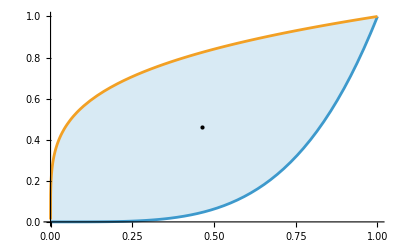

```mathematica
Plot[
{f1[x], f2[x]},
{x, xMin, xMax},
Filling -> {1 -> {2}},
Epilog->{
PointSize[Large],
Point[{xCM, yCM}]
}
]
```

### 5) Wyznaczyć korzystając z funkcji RegionCentroid dla reg zdefiniowanego w 2)

```mathematica
RegionCentroid[reg]
```

{25/54,25/54}

### 6) Całki z 3) można uprościć do wzorów zawierających pojedynczą całkę po

Uprość wzory z 3) i sprawdź czy dostajesz poprawny wynik.

```mathematica
xCM = Integrate[x/S (f2[x] - f1[x]) , {x, xMin, xMax}]
```

25/54

```mathematica
yCM = Integrate[1/(2S) (f2[x]^2 - f1[x]^2), {x, xMin, xMax}]
```

25/54